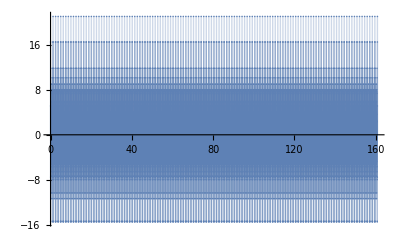

```mathematica
signalData = SetPrecision[#, 16] & /@ ReadList["D:\\учеба\\фоит\\IDZ3\\1.txt", Real];

deltaT = SetPrecision[0.0196349540849362, 16];
n = Length[signalData];

xValues = Table[deltaT * (i - 1), {i, 1, n}];
(*ListPlot[Transpose[{xValues, signalData}], Filling->Axis, PlotRange -> {{0, deltaT * 64}, Automatic}]*)
ListPlot[Transpose[{xValues, signalData}], Filling->Axis, PlotRange -> {{0, deltaT * n}, Automatic}]
```

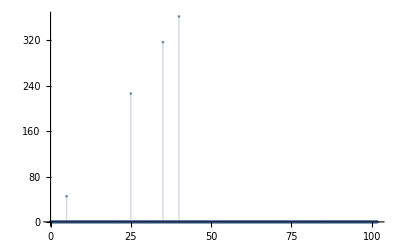

```mathematica
fourierSignalData = Fourier[signalData];
df = 1 / (deltaT * n);

spectrumData = Table[{2π * df * (i - 1), Abs@fourierSignalData[[i]]}, {i, 1, 2607}];
ListPlot[spectrumData, Filling->Axis]
```

0.176326755119

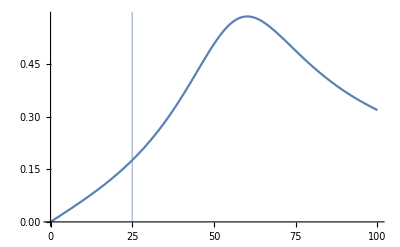

```mathematica
harmonica = Select[spectrumData, #[[2]] > 1 &][[2]];

L1 = SetPrecision[12.5027244377969, 15];
L2 = SetPrecision[0.732314055423997, 15];
C1 = SetPrecision[0.0000109944353937182, 15];
C2 = SetPrecision[0.0000118252105681497, 15];
R1 = SetPrecision[105.380407917585, 15];
R2 = SetPrecision[33.7954683489311, 15];
R3 = SetPrecision[1013.44027561406, 15];
R4 = SetPrecision[511.280315438187, 15];


Z1[omega_]= R4 + 1 / (I omega C2); 
Z2[omega_]= 1/(I omega C1)+R2 + I omega L2 + R3;
Z[omega_] = 1 /(1 / Z1[omega] + 1 / Z2[omega]);
I1[omega_] = Uin / (R1 + I omega L1 + Z[omega]);
U[omega_] = I1[omega] * Z[omega];
Ir4c2[omega_] = U[omega] / Z1[omega];
Uout[omega_] = Ir4c2[omega] * R4;
H[omega_]= Uout[omega] / Uin;

Abs@H[harmonica[[1]]]
Show[Plot[Abs@H[omega], {omega, 0, 100}], 
 ListPlot[{harmonica}, Filling -> Axis]]
```